# Mediator Model Analysis

Isaac R. Wang

This code analysis the freeze-in and out for the mediator model.

## Prepare

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

```mathematica
MakeBoxes[p1,TraditionalForm]:="p_1";
MakeBoxes[p2,TraditionalForm]:="p_2";
MakeBoxes[p3,TraditionalForm]:="p_3";
MakeBoxes[p4,TraditionalForm]:="p_4";
MakeBoxes[mχ,TraditionalForm]:="m_χ";
MakeBoxes[mν,TraditionalForm]:="m_ν";
MakeBoxes[mϕ,TraditionalForm]:="m_ϕ";
MakeBoxes[m1,TraditionalForm]:="m_1";
MakeBoxes[m2,TraditionalForm]:="m_2";
MakeBoxes[yχ,TraditionalForm]:="y_χ";
MakeBoxes[yν,TraditionalForm]:="y_ν";
MakeBoxes[αχ,TraditionalForm]:="α_χ";
MakeBoxes[αν,TraditionalForm]:="α_ν";
MakeBoxes[gH,TraditionalForm]:="g_H";
MakeBoxes[mpl,TraditionalForm]:="m_pl";
MakeBoxes[E1,TraditionalForm]:="E_1";
MakeBoxes[vsq,TraditionalForm]:="v^2";
MakeBoxes[Γϕ,TraditionalForm]:="Γ_ϕ";
MakeBoxes[Y∞,TraditionalForm]:="Y_∞";
MakeBoxes[Yf,TraditionalForm]:="Y_f";
MakeBoxes[xf,TraditionalForm]:="x_f";
MakeBoxes[Nν,TraditionalForm]:="N_ν";
MakeBoxes[Nχ,TraditionalForm]:="N_χ";
$Assumptions={{2mχ-mϕ,s-4 mχ^2,mχ,mϕ,T,s,y,gH,mpl}>0};
GeV=10^3;(*Unit MeV*)
```

## Scattering amplitude and cross section

The Lagrangian of the model is

L=y_χ χ̄ ϕ_μ γ^μ P_L χ+y_ν ν̄ ϕ_μ γ^μ P_L ν

The scattering amplitude can be computed in the following way.

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-p3,-p4,m1,m1,m2,m2];
M=yχ yν(SpinorVBar[p2,m1].GA[μ].GA[7].SpinorU[p1,m1])MT[μ,ν]/(SP[p1+p2,p1+p2]-mϕ^2)(SpinorUBar[p3,m2].GA[ν].GA[7].SpinorV[p4,m2])//Contract;
Msq=FermionSpinSum[ComplexConjugate[M]*M,ExtraFactor->1/4]//DiracSimplify//Simplify
```

(y_ν^2 y_χ^2 (m_1^2+m_2^2-u)^2)/((m_ϕ^2-s)^2)

The 2 couplings are always connected with each other here. So this time we just assume they are the same.
One feature of this amplitude is that we are using general m_1 and m_2. In specific status, we should pick which one is which.

```mathematica
(*ν -> χ*)
pi=(√s)/2;
pf=√(s/4-mχ^2);
Msqνtoχ=Msq/.{m1->0,m2->mχ,yν->y,yχ->y,u->mχ^2-2(s/4+pi pf cosθ)};
σνχ[mχ_,mϕ_,y_,s_]=1/(32π s)pf/pi Integrate[Msqνtoχ,{cosθ,-1,1}]//Simplify
(*χ -> ν*)
pf=(√s)/2;
pi=√(s/4-mχ^2);
Msqχtoν=Msq/.{m1->mχ,m2->0,yν->y,yχ->y,u->mχ^2-2(s/4+pi pf cosθ)};
σχν[mχ_,mϕ_,y_,s_]=1/(32π s)pf/pi Integrate[Msqχtoν,{cosθ,-1,1}]//Simplify
```

(y^4 √(1-(4 m_χ^2)/s) (s-m_χ^2))/(48 π (m_ϕ^2-s)^2)

(y^4 (s-m_χ^2))/(48 π √(1-(4 m_χ^2)/s) (m_ϕ^2-s)^2)

## DM Production and equilibrium

### Collision terms

The 2-2 collision terms is derived by P. Gondolo and G. Gelmini as

C_(2-2)=T/(32 π^4)∫_(4 m_χ^2)^∞ √s(s-4 m_1^2)σ K_1((√s)/T)ⅆs

where the m_χ is the dark matter mass and the m_1 is the mass of the incoming particle.

For the production, ν->χ case, we have m_1=0.

Since we always have s>4 m_χ^2 to get kinematically allowed, we can take the approximation s >> m_χ^2, this should be correct especially for large energy region.

```mathematica
Cnum‵prod[mχ_,mϕ_,y_,T_]:=T/(32 π^4)NIntegrate[(σνχ[mχ,mχ,y,s])√s s BesselK[1,(√s)/T],{s,4 mχ^2,∞}](*Following the numerical integration directly*)
```

```mathematica
Cana‵prod[mχ_,y_,T_]=T/(32 π^4)Integrate[(σνχ[mχ,mχ,y,s])*(s-mχ^2)/s*√s s BesselK[1,(√s)/T],{s,4 mχ^2,∞}](*Take approximation, remove Subscript[m, χ]^2 and Subscript[m, ϕ]^2, only keep 4 Subscript[m, χ]^2*)
```

(m_χ^2 T^2 y^4 (1m_χ/T)^2)/(384 π^5)

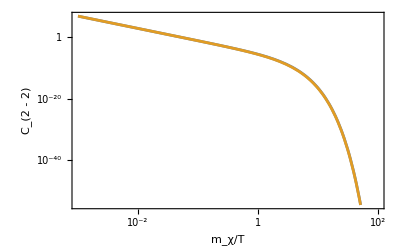

```mathematica
Plot[{Log10[Cnum‵prod[1,1.5,1,1/10^logTinv]],Log10[Cana‵prod[1,1,1/10^logTinv]]},{logTinv,-3,2},FrameTicks->{{LogTicks[-60,10,10],True},{LogTicks[-4,3,1],True}},FrameLabel->{"m_χ/T","C_(2 - 2)"},Epilog->{Inset[Framed[Column[{LineLegend[{ColorData[97,1],ColorData[97,2]},{Style["Numerical",FontFamily->"Times",FontSize->16],Style["Approx",FontFamily->"Times",FontSize->16]}]}],RoundingRadius->5],Scaled[{0.2,0.2}]]}]
```

This shows that the approximation behaves pretty good for the production part.

The high-T and low-T expansion can provide even better intuition.

```mathematica
ChighT[y_,T_]=Series[Cana‵prod[mχ,y,T],{mχ,0,0}]//Normal
ClowT[mχ_,y_,T_]=Series[Cana‵prod[mχ,y,T],{T,0,3}]//Normal
```

(T^4 y^4)/(384 π^5)

(m_χ T^3 y^4 ⅇ^(-(2 m_χ)/T))/(768 π^4)

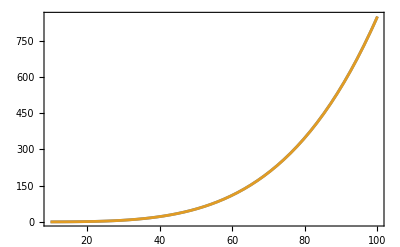

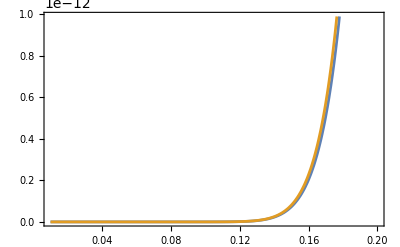

```mathematica
Plot[{ChighT[1,T],Cana‵prod[1,1,T]},{T,10,100}]
Plot[{ClowT[1,1,T],Cana‵prod[1,1,T]},{T,0.01,0.2}]
```

Next let’s talk about the back reaction.

```mathematica
T/(32 π^4)Integrate[(σχν[mχ,mχ,y,s])*(s-mχ^2)/s*√s(s-4 mχ^2) BesselK[1,(√s)/T],{s,4 mχ^2,∞}](*Test the back reaction*)
```

(m_χ^2 T^2 y^4 (1m_χ/T)^2)/(384 π^5)

The back reaction is the same expression.

```mathematica
Cnum‵back[mχ_,mϕ_,T_,y_]:=T/(32 π^4)NIntegrate[(σχν[mχ,mχ,y,s])√s(s-4 mχ^2) BesselK[1,(√s)/T],{s,4 mχ^2,∞}]
```

```mathematica
Plot[{Log10[Cnum‵back[1,1.5,1/10^logTinv,1]],Log10[Cana‵prod[1,1/10^logTinv,1]]},{logTinv,-3,2},FrameTicks->{{LogTicks[-60,10,10],True},{LogTicks[-4,3,1],True}},FrameLabel->{"m_χ/T","C_(2 - 2)"},Epilog->{Inset[Framed[Column[{LineLegend[{ColorData[97,1],ColorData[97,2]},{Style["Numerical",FontFamily->"Times",FontSize->16],Style["Approx",FontFamily->"Times",FontSize->16]}]}],RoundingRadius->5],Scaled[{0.2,0.2}]]}]
```

-Graphics-

So the back reaction also has very good behavior.

In this section, we concluded that the production and back reaction collision term has the same approximation form, and they have good behaviors. The difference of the collision terms of two directions then come from the particle density.

#### Bessel Function

```mathematica
(Series[BesselK[1,1/r],{r,0,4}]//Normal)/.{r->1/x}
(Series[BesselK[2,1/r],{r,0,4}]//Normal)/.{r->1/x}
```

ⅇ^-x ((3 √(π/2))/(8 x^(3/2))-(15 √(π/2))/(128 x^(5/2))+(105 √(π/2))/(1024 x^(7/2))+(√(π/2))/(√x))

ⅇ^-x ((15 √(π/2))/(8 x^(3/2))+(105 √(π/2))/(128 x^(5/2))-(315 √(π/2))/(1024 x^(7/2))+(√(π/2))/(√x))

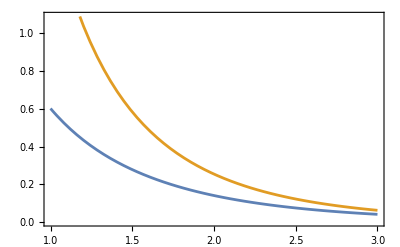

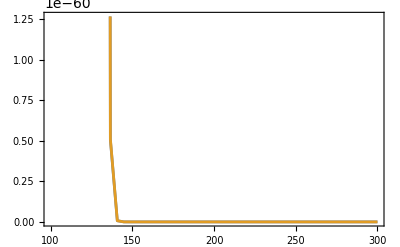

```mathematica
Plot[{BesselK[1,x],BesselK[2,x]},{x,1,3}]
Plot[{BesselK[1,x],BesselK[2,x]},{x,100,300}]
```

### Production computation

The production for χ particle follows the high-T limit of the production collision term at the early time. The Boltzmann equation becomes

(ⅆ(n a^3))/ⅆa=a^2/(H(a))C_p(T)

To perform this integral we need to switch from a to T at first. We can write a=κ/T, then this equation becomes

ⅆ/ⅆT(n a^3)ⅆT/ⅆa=ⅆ/ⅆT(n a^3)(-T^2/κ)=(κ^2/T^2)/(g_H T^2/m_pl)C_p(T)

Here we use that H=g_H T^2/m_pl where g_H=√(8 π^3 g_*/90) is the coefficient of the Hubble rate. Performing this integral we have

n a^3=κ^3 m_pl/g_H∫(C_p(T'))/(T')^6 ⅆT'

Then

n=T^3 m_pl/g_H∫(C_p(T'))/(T')^6 ⅆT'

The integration limit can tell us something. If we stop at some certain temperature, this tells us how much n_χ has been produced so far.
If we use high-T form of the collision term here, we can see that the number density continues growing without slowing down.
On the other hand, if we perform this integral all along the time from 0 to ∞, this number can performs as the maximal value of the production.
The real world never reaches the maximum due to that the back reaction becomes more effective and the neutrino energy is lost when the number getting close to the maximum. Approximately, if the high-T integration reaches the maximum value, this temperature can be approximated as “T_prod”, referred to as the point where the production stops and the DM enters equilibrium. In reality, the production curve will be bent lower (slower production) at the vicinity of this temperature, and the actual equilibrium time is later than “T_prod”. But this difference is small, as we will show later by numerical computation. Here let’s perform the analytical approximation here.

```mathematica
Clear[Nν,Nχ]
```

```mathematica
nχ[y_,T_]=Nν T^3 mpl/gH Integrate[ChighT[y,T‵]/(T‵)^6,{T‵,T,∞}]//Normal
nχmax[mχ_,y_,T_]=Nν T^3 mpl/gH Integrate[1/(T‵)^6 Cana‵prod[mχ,y,T‵],{T‵,0,∞},Assumptions->{mχ>0}]//Normal
```

(m_pl N_ν T^2 y^4)/(384 π^5 g_H)

(m_pl N_ν T^3 y^4)/(4096 π^3 g_H m_χ)

Let the production equal to the max, we can have the temperature at which the χ is fully produced.

```mathematica
Tprod[mχ_]=T/.Solve[nχmax[mχ,y,T]==nχ[y,T],T][[-1]]//Normal
```

(32 m_χ)/(3 π^2)

```mathematica
nχ[y,Tprod[mχ]]
nχmax[mχ,y,Tprod[mχ]]
```

(8 m_pl m_χ^2 N_ν y^4)/(27 π^9 g_H)

(8 m_pl m_χ^2 N_ν y^4)/(27 π^9 g_H)

Note: this maximal value may not be achieved. The n_χ cannot exceeds the equilibrium value, i.e. the MB distribution.

```mathematica
nMB[mχ_,T_]:=2 1/(2 π^2)mχ^2 T BesselK[2,mχ/T];
(y/.Solve[nχmax[mχ,y,Tprod[mχ]]==nMB[mχ,T]//Simplify,y,Assumptions->{}][[1]])//Simplify
```

((3/2)^(3/4) π^(7/4) g_H^(1/4) T^(1/4) (2m_χ/T)^(1/4))/(m_pl^(1/4) N_ν^(1/4))

This is the maximal coupling we can have for freeze-in mechanism for a certain m_χ.

### ΔN_eff

The N_eff should not exceeds the observed limit at the time of BBN, we roughly takes it to be 1 MeV. The upper limit for the n_χ can be translated roughly into n_ν/10.

```mathematica
nνeq[T_]:=2(3 Zeta[3])/(4 π^2)T^3;(*dof g=2*)
Tνnν[n_]:=(4 π^2/(3 Zeta[3]*2)n)^(1/3);
```

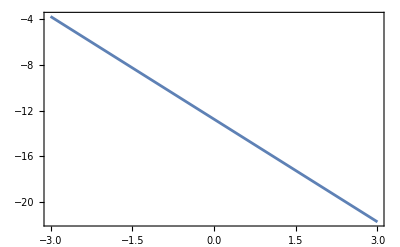

```mathematica
Plot[Log10[nνeq[10^-4/10^logx]],{logx,-3,3}]
```

```mathematica
Collect[nχ[y,T]==1/10 nνeq[T],y,FullSimplify]
```

(m_pl N_ν T^2 y^4)/(384 π^5 g_H)==(3 T^3 3)/(20 π^2)

```mathematica
ymax=(y/.Solve[Collect[nχ[y,T]==1/10 nνeq[T],y,FullSimplify],y,Assumptions->{}][[-1]])
ymax/.{gH->√(8 π^3/90*3.91),mpl->1.22*10^19,T->10^-4,Nν->3}
```

(2 √3 π^(3/4) g_H^(1/4) T^(1/4) ((2 3)/5)^(1/4))/(m_pl^(1/4) N_ν^(1/4))

0.0000117798

A little bit more than 10^-5.

### Plot

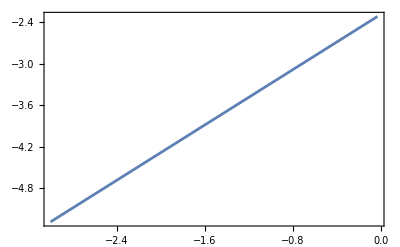

```mathematica
ytest=10^-6;
mtest=10^-4;
Plot[Log10[nχ[ytest,mtest/10^logx]/nνeq[mtest/10^logx]]/.{gH->√(8 π^3/90 3.91),Nν->3,mpl->1.22*10^19*GeV},{logx,-3,Log10[mtest/Tprod[mtest]]}]
```

## DM Freeze-out regime

In the freeze-out regime, i.e. some time after the equilibrium, the back reaction collision term dominates. In this case, the Boltzmann equation becomes

(ⅆ(n a^3))/ⅆa=-a^2/H C_d=-a^2/H<σ v>(n_χ^2-n_eq^2)

The thermal-averaged cross section can be expressed in terms of the one at NR limit, which is

```mathematica
σv0[mχ_,mϕ_,y_]=(σχν[mχ,mϕ,y,s]*√(s/4-mχ^2)4/(√s)//Simplify)/.{s->4 mχ^2}
```

(m_χ^2 y^4)/(8 π (m_ϕ^2-4 m_χ^2)^2)

Let’s perform under the traditional freeze-out solution framework. The Boltzmann equation can be written as

ⅆY/ⅆx=-λ/x^2(Y^2-Y_eq^2)

Here we define Y=n/T^3, λ=m_pl m <σ v>_0/(g_H). Here the cross-section is computed in the NR limit and only s-wave contribution is included. There is no analytical solution for this equation, however we know that Y_eq becomes negligible after some point of x. In this limit, we have

ⅆY/ⅆx=-λ/x^2 Y^2

```mathematica
yapprox[x_]=y[x]/.DSolve[{y'[x]==-λ/x^2 y[x]^2,y[∞]==Y∞},y[x],x][[1]]
```

(Y_∞ x)/(x-λ Y_∞)

The lower limit of x for this equation to make sense is simply

x=λ Y_∞

We define this to be x_f, where the DM freezes out. For a smaller x, the particle is in equilibrium. For large enough x, this approximated solution is justified. For some middle point, we need some trick to express between them. Determine it by

Y=(Y_∞x)/(a x+b)

```mathematica
Ymiddle[x_]=(Y∞ x)/(a x+b)/.Solve[{Y∞ xf/(a xf+b)==Yf,Y∞ (2xf)/(2a xf+b)==(Y∞ 2 xf)/(2xf-λ Y∞)},{a,b}]/.{Y∞->xf/λ}//Simplify
```

{-(x_f Y_f x)/(x_f (λ Y_f-2 x_f)+x (x_f-λ Y_f))}

```mathematica
Collect[Denominator[Ymiddle[x]//Simplify]/(xf),x,Simplify]
```

{x (1-(λ Y_f)/x_f)-2 x_f+λ Y_f}

So the final result is

Y_mid=(Y_f x)/(x ((λ Y_f)/x_f-1)+x_f(2-λ Y_f/x_f))

In summary, we have

Y=(Y_∞ x)/(x-λ Y_∞), x>2 x_f
Y=Y_eq,x<x_f
Y=(Y_f x)/(x ((λ Y_f)/x_f-1)+x_f(2-λ Y_f/x_f)),x_f<x<2 x_f

What is the equilibrium value? We immediately know that Y_eq must behave as x^2 K_2(x), we can set the pre-factor so that it agrees with the produced amount at T_prod.
If the dark matter has not reached the equilibrium at T_prod, the number is nothing but the produced number there. But if it exceeds this amount, that means

```mathematica
Clear[mpl]
```

```mathematica
xprod[mχ_]=mχ/Tprod[mχ]
Yprod[mχ_,y_]=nχ[y,Tprod[mχ]]/Tprod[mχ]^3
Yeq[mχ_,y_,x_]=nMB[mχ,mχ/x] x^3/mχ^3
```

(3 π^2)/32

(m_pl N_ν y^4)/(4096 π^3 g_H m_χ)

(x^2 2x)/π^2

To calculate Y, the remaining question is the x_f.

```mathematica
λ[mχ_,mϕ_,y_]=(mpl mχ)/gH σv0[mχ,mϕ,y];
xf[mχ_,mϕ_,y_]:=x/.FindRoot[x==Log[(λ[mχ,mϕ,y]/π^2)/(√x)]/.{gH->√(8 π^3/90 3.91),Nν->3,mpl->1.22*10^19*GeV},{x,20}]//Re
```

```mathematica
mχtest=10^-4;
mϕtest=10^-4;
ytest=10^-5;
xf[mχtest,mϕtest,ytest]
```

4.37668

```mathematica
Yfo[mχ_,mϕ_,y_,xfo_,x_]:=Piecewise[{{Yeq[mχ,y,x],x<=xfo},{(Yeq[mχ,y,xfo]*x)/(x((λ[mχ,mϕ,y]Yeq[mχ,y,xfo])/xfo-1)+xfo(2-(λ[mχ,mϕ,y]Yeq[mχ,y,xfo])/xfo)),xfo<x<=2xfo},{(x*xfo/λ[mχ,mϕ,y])/(x-xfo),x>2xfo}}]/.{gH->√(8 π^3/90 3.91),Nν->3,mpl->1.22*10^19*GeV};
```

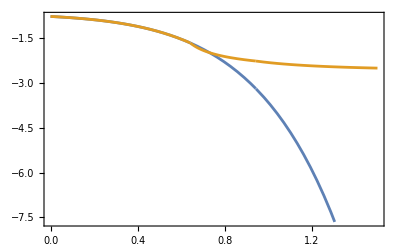

```mathematica
mχtest=10^-4;
mϕtest=10^-4;
ytest=10^-5;
Plot[{Log10[Yeq[mχtest,ytest,10^logx]],Log10[Yfo[mχtest,mϕtest,ytest,xf[mχtest,mϕtest,ytest],10^logx]]},{logx,0,1.5}]
```

### Numerical computation

```mathematica
SolveFreezeout[mχ_,mϕ_,y_,bd_]:=Block[{mpl,gH,Nν,s0,ρDM0,ρcrit,ΩDMhsq,sol,Yinf,inf},
gH=√((8 π^3)/90 3.91);
mpl=1.24*10^19*GeV;
Nν=3;
inf=1000;
sol=lnY/.NDSolve[{ⅇ^lnY[x] lnY'[x]==(-λ[mχ,mϕ,y])/x^2(ⅇ^lnY[x]-Yeq[mχ,y,x])(ⅇ^lnY[x]+Yeq[mχ,y,x]),ⅇ^lnY[bd]==Yeq[mχ,y,bd]},lnY,{x,bd,inf}][[1]];
Yinf=(inf*ⅇ^sol[inf])/(inf+λ[mχ,mϕ,y]*ⅇ^sol[inf]);
s0=2891.2;
ρDM0=s0 mχ Yinf;
ρcrit=1.05*10^-5;
ΩDMhsq=ρDM0/ρcrit;
{sol,ΩDMhsq}
]
```

```mathematica
{sol,Ω}=SolveFreezeout[10^-4,10^-4,10^-5,0.01]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{InterpolatingFunction[…],77.4088}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{InterpolatingFunction[…],77.4088}

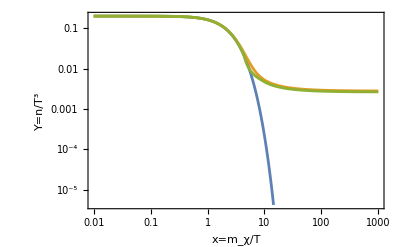

```mathematica
mχtest=10^-4;
mϕtest=10^-4;
ytest=10^-5;
{sol,Ω}=SolveFreezeout[mχtest,mϕtest,ytest,0.01]
LogLogPlot[{Yeq[mχtest,ytest,x]/.{gH->√(8 π^3/90 3.91),Nν->3,mpl->1.22*10^19*GeV},(ⅇ^sol[x]),Yfo[mχtest,mϕtest,ytest,xf[mχtest,mϕtest,ytest],x]},{x,0.01,1000},FrameLabel->{"x=m_χ/T","Y=n/T^3"}]
```

So it agrees with the previous computation.

However, why the x is smaller than expected? The coupling is already large but we have x<20. If the coupling is smaller than the constraint for the ΔN_eff, i.e. y<10^-5, the x should be very small and DM density should be very large. This does not make sense.

## Combine all the periods

The first thing we need to discuss is whether the equilibrium is achieved.

```mathematica
Y[mχ_,mϕ_,y_,Tp_,xfo_,x_]:=If[(nχ[y,Tprod[mχ]]>nMB[mχ,Tprod[mχ]])/.{gH->√(8 π^3/90 3.91),Nν->3,mpl->1.22*10^19*GeV},
xeq=(10^logx/.FindRoot[(nχ[y,mχ/10^logx]==nMB[mχ,mχ/10^logx])/.{gH->√(8 π^3/90 3.91),Nν->3,mpl->1.22*10^19*GeV},{logx,-2}]);Piecewise[{{nχ[y,mχ/x] x^3/mχ^3,x<=xeq},{Yfo[mχ,mϕ,y,xfo,x],x>xeq},{(x*xfo/λ[mχ,mϕ,y])/(x-xfo),x>2xfo}}]/.{gH->√(8 π^3/90 3.91),Nν->3,mpl->1.22*10^19*GeV},Piecewise[{{nχ[y,mχ/x] x^3/mχ^3,x<=xprod[mχ]},{Yprod[mχ,y],x>xprod[mχ]}}]];
```

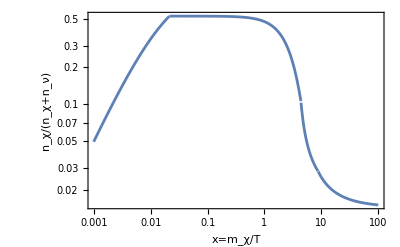

```mathematica
ytest=10^-5;
mχtest=10^-4;
mϕtest=10^-4;
theoryplot=LogLogPlot[Y[mχtest,mϕtest,ytest,Tprod[mχtest],xf[mχtest,mϕtest,ytest],x] mχtest^3/x^3 1/(nνeq[mχtest/x]+Y[mχtest,mϕtest,ytest,Tprod[mχtest],xf[mχtest,mϕtest,ytest],x] mχtest^3/x^3),
{x,0.001,100},FrameLabel->{"x=m_χ/T","n_χ/(n_χ+n_ν)"}]
```